## Datenimport

```mathematica
rawDataAuthors=Import["C:\\Users\\martin\\github_repos\\THERMO-EDA\\v3\\kritische_micellen_konz.csv"];
volume=Transpose[Drop[rawDataAuthors,1]][[1]];
lfVeWater=Transpose[Drop[rawDataAuthors,1]][[2]];
lfNaCl=Transpose[Drop[rawDataAuthors,1]][[3]];
```

## Fitting lfVeWater

FittedModel[16.5602+0.339668 x]

16.5602+0.339668 x

FittedModel[364.23+0.141503 x]

364.23+0.141503 x

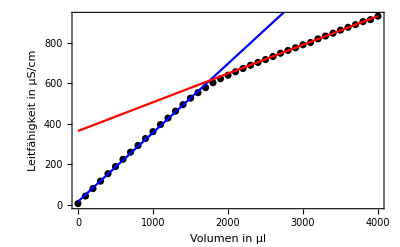

```mathematica
xyPairs=Transpose[{volume,lfVeWater}];
xyPairsT1=Take[xyPairs,{1,18}];
linearModelT1=LinearModelFit[xyPairsT1,x,x]
linearFuncT1=linearModelT1["BestFit"]

xyPairsT2=Take[xyPairs,{30,41}];
linearModelT2=LinearModelFit[xyPairsT2,x,x]
linearFuncT2=linearModelT2["BestFit"]

(*Visualize the fit*)
Show[ListPlot[xyPairs,PlotStyle->Black],Plot[linearModelT1[x],{x,0,4000},PlotStyle->Blue],Plot[linearModelT2[x],{x,0,4000},PlotStyle->Red],Frame->True,FrameLabel->{"Volumen in µl","Leitfähigkeit in µS/cm"}
]
```

## CMC SDS in VE-Water

```mathematica
sol=Solve[linearFuncT1==linearFuncT2];
interceptT1T2=x/. sol[[1]]
```

1754.45

```mathematica
cmc=0.058/(interceptT1T2/1000000)
```

33.0588

## Fitting lfNaCl

FittedModel[1828.08+0.305119 x]

1828.08+0.305119 x

FittedModel[1995.91+0.127273 x]

1995.91+0.127273 x

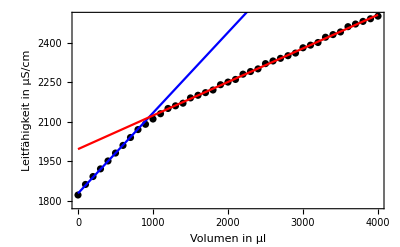

```mathematica
xyPairs=Transpose[{volume,lfNaCl}];
xyPairsT1=Take[xyPairs,{1,8}];
linearModelT1=LinearModelFit[xyPairsT1,x,x]
linearFuncT1=linearModelT1["BestFit"]

xyPairsT2=Take[xyPairs,{30,41}];
linearModelT2=LinearModelFit[xyPairsT2,x,x]
linearFuncT2=linearModelT2["BestFit"]

(*Visualize the fit*)
Show[ListPlot[xyPairs,PlotStyle->Black],Plot[linearModelT1[x],{x,0,4000},PlotStyle->Blue],Plot[linearModelT2[x],{x,0,4000},PlotStyle->Red],
Frame->True,FrameLabel->{"Volumen in µl","Leitfähigkeit in µS/cm"}
]
```

## Calc SDS in NaCl

```mathematica
sol=Solve[linearFuncT1==linearFuncT2];
interceptT1T2=x/. sol[[1]]
```

943.656

```mathematica
cmc=0.058/(interceptT1T2/1000000)
```

61.4631